```mathematica
<<SARAH`
```

Remove::rmptc: Symbol JLink`Fields is Protected and cannot be removed.

SARAH 4.15.3

by Florian Staub, Mark Goodsell and Werner Porod, 2020

contributions by M. Gabelmann, K. Nickel

References:

Comput.Phys.Commun.181 (2010) 1077-1086. (arXiv:0909.2863)

Comput.Phys.Commun.182 (2011) 808-833. (arXiv:1002.0840)

Comput.Phys.Commun.184 (2013) 1792-1809. (arXiv:1207.0906)

Comput.Phys.Commun.185 (2014) 1773-1790. (arXiv:1309.7223)

Eur.Phys.J.C 74 (2014) 8, 2992 (arXiv:1405.1434)

Eur.Phys.J.C 75 (2015) 1, 32 (arXiv:1411.0675)

Eur.Phys.J.C 75 (2015) 6, 290 (arXiv:1503.03098)

Eur.Phys.J.C 77 (2017) 11, 758 (arXiv:1703.09237

Eur.Phys.J.C 77 (2017) 11, 757 (arXiv:1706.05372)

Eur.Phys.J.C 78 (2018) 8, 649 (arXiv:1805.07306)

Download and Documentation:

http://sarah.hepforge.org

Start evaluation of a model with:

Start["Name of Model"]

e.g. Start["MSSM"] or Start["NMSSM","CKM"]

To get a list with all installed models, use ShowModels

```mathematica
Start["SSDMv2"]
```

Preparing arrays

... checking Directory: /home/lessa/.Mathematica/Applications/SARAH-4.15.3/Models/

Model files loaded

Model    : SSDMv2

Author(s): Andre Lessa (based on SM model by F.Staub and SSDM by Diego Restrepo and arXiv:2404.19057)

Date     : 2024-07-02

*******************************************************

Loading Susyno functions for the handling of Lie Groups

Based on Susyno v.2.0 by Renato Fonseca (1106.5016)

webpage: web.ist.utl.pt/renato.fonseca/susyno.html

*******************************************************

Initialization

Checking model files:

Initialize gauge groups:

Initialize field:

Preprocessing necessary information:

Checking for anomalies:

Derive Lagrangian

Calculate kinetic Terms

... for scalars: /8 ()

... for fermions: /8 ()

Calculate vector self-interactions: /3 ()

Calculate gauge transformations: /11 ()

Eleminate sums

Calc Complete Lagrangian

Evolve States: GaugeES

Adding terms to the Lagrangian:

... adding: -Yu H.u.q-Yd conj[H].d.q-Ye conj[H].e.l ()

... adding: -1/2 MS12 S1.S1-(MS22 S2.S2)/2-mu2 conj[H].H-Lam14 S1.S1.S1.S1-Lam31 S1.S1.S1.S2-Lam22 S1.S1.S2.S2-LamH1 S1.S1.conj[H].H-Lam13 S1.S2.S2.S2-LamH12 S1.S2.conj[H].H-Lam24 S2.S2.S2.S2-LamH2 S2.S2.conj[H].H-1/2 Lambda1 conj[H].H.conj[H].H ()

Rotate Lagrangian: /14

Derive ghost terms:

... generate gauge fixing terms: /3 ()

... calculate Ghost interactions

Calc Mixings of Matter Fields

Save information ()

Evolve States: EWSB

Parametrize Higgs Sector

Update gauge transformations: /19 ()

Calc mass matrices gauge sector: /2()

Update gauge transformations: /26 ()

Rotate Lagrangian: /14

Derive ghost terms:

... generate gauge fixing terms: /4 ()

... calculate Ghost interactions

Calc Mixings of Matter Fields

Calculate mass matrices /3 ()

Update gauge transformations: /28 ()

Calculate Tadpole Equations

Save information ()

Finishing

Calculate final Lagrangian

Cleaning up

... add matrix products

... checking for massless particles

... calculating tree level masses ()

... simplify mass matrices

Numerical calculations (if necessary)

... checking for spectrum file:

... reading parameter values and dependences

... calculate mixing matrices

Checking for CP even and odd scalars

All Done. SSDMv2 is ready!

(Model initialized in 9.24039s)

Are you unfamiliar with SARAH? Use SARAH`FirstSteps

```mathematica
Particles[GaugeES]
```

{{VB,1,1,V,{{lorentz,4}}},{gB,1,1,G,{}},{VWB,1,3,V,{{generation,3},{lorentz,4}}},{gWB,1,3,G,{{generation,3}}},{VG,1,1,V,{{color,8},{lorentz,4}}},{gG,1,1,G,{{color,8}}},{H0,1,1,S,{}},{Hp,1,1,S,{}},{ss1,1,1,S,{}},{ss2,1,1,S,{}},{dL,1,3,F,{{generation,3},{color,3}}},{uL,1,3,F,{{generation,3},{color,3}}},{eL,1,3,F,{{generation,3}}},{vL,1,3,F,{{generation,3}}},{dR,1,3,F,{{generation,3},{color,3}}},{uR,1,3,F,{{generation,3},{color,3}}},{eR,1,3,F,{{generation,3}}}}

```mathematica
Masses[GaugeES];
Masses[EWSB]
```

{Mass[VG]→MassGiven[VG],Mass[gG]→MassGiven[gG],Mass[Hp]→MassGiven[Hp],Mass[ss1]→MassRead[ss1],Mass[ss2]→MassRead[ss2],Mass[Fv[1]]→MassGiven[Fv[1]],Mass[Fv[2]]→MassGiven[Fv[2]],Mass[Fv[3]]→MassGiven[Fv[3]],Mass[Ah]→MassGiven[Ah],Mass[hh]→MassRead[hh],Mass[VP]→MassGiven[VP],Mass[VZ]→MassGiven[VZ],Mass[gP]→MassGiven[gP],Mass[gZ]→MassGiven[gZ],Mass[gWp]→MassGiven[gWp],Mass[gWpC]→MassGiven[gWpC],Mass[Fd[1]]→MassGiven[Fd[1]],Mass[Fd[2]]→MassGiven[Fd[2]],Mass[Fd[3]]→MassGiven[Fd[3]],Mass[Fd[1]]→MassGiven[Fd[1]],Mass[Fd[2]]→MassGiven[Fd[2]],Mass[Fd[3]]→MassGiven[Fd[3]],Mass[Fu[1]]→MassGiven[Fu[1]],Mass[Fu[2]]→MassGiven[Fu[2]],Mass[Fu[3]]→MassGiven[Fu[3]],Mass[Fu[1]]→MassGiven[Fu[1]],Mass[Fu[2]]→MassGiven[Fu[2]],Mass[Fu[3]]→MassGiven[Fu[3]],Mass[Fe[1]]→MassGiven[Fe[1]],Mass[Fe[2]]→MassGiven[Fe[2]],Mass[Fe[3]]→MassGiven[Fe[3]],Mass[Fe[1]]→MassGiven[Fe[1]],Mass[Fe[2]]→MassGiven[Fe[2]],Mass[Fe[3]]→MassGiven[Fe[3]]}

```mathematica
Lagrangian[GaugeES];
```

```mathematica
CalcRGEs[TwoLoop->True];
```

Calculate non-supersymmetric RGEs

Initializing Invariants...

Fermion bilinear

(Time needed so far: 5.70113s)

Fermion chains

(Time needed so far: 36.9771s)

Scalar bilinear

... 1-loop

... 2-loop

(Time needed so far: 71.6525s)

Scalar quartic

... 1-loop

... 2-loop

(Time needed so far: 181.666s)

Scalar cubic

... 1-loop

... 2-loop

(Time needed so far: 181.666s)

All necessary invariants are ready (Time needed: 181.666s)

Calculation of beta functions...

Calculate Beta Functions for Gauge Couplings

Calculating /3.()

Calculate anomalous dimensions of scalars

Calculating /4.()

Calculate hat(gamma) for running VEVs

Calculating /4.()

Calculate anomalous dimensions of fermions

Calculating /5.()

Calculate Beta Functions for Yukawa-like interactions

Calculating /3.()

Calculate Beta Functions for bilinear Fermion interactions

Nothing to do.

Calculate Beta Functions for scalar 4-point interactions

Calculating /9.()

Calculate Beta Functions for scalar 3-point interactions

Nothing to do.

Calculate Beta Functions for bilinear scalar interactions

Calculating /3.()

Calculate Beta Functions for VEVs

Calculating /1.()

Writing Mathematica code to evaluate RGEs

Finished with the calculation of the RGEs. Time needed: 349.196s

The results are saved in /home/lessa/.Mathematica/Applications/SARAH-4.15.3/Output/SSDMv2/RGEs/

```mathematica
ModelOutput[GaugeES,WriteTeX-> True,FeynmanDiagrams->True]
```

Checking model for missing definitions

Transpose::nmtx: The first two levels of {} cannot be transposed.

Generate Directories

Building Particle List

Calculate all vertices

Three Scalar - Interactions

Found 0 potential vertices. Calculating /0)

Four Scalar - Interactions

Found 14 potential vertices. Calculating /14 . ()

Two Scalar - One Vector Boson - Interactions

Found 6 potential vertices. Calculating /6 . ()

Vertex::ChargeViolating: Non-zero result for {Hp,conj[H0],VWB} vertex which violates charge. (This might just be a problem with simplifying the vertex, but could also point towards a mistake in the implementation.)

One Scalar - Two Vector Boson - Interactions

Found 0 potential vertices. Calculating /0)

Two Scalar - Two Vector Boson - Interactions

Found 10 potential vertices. Calculating /10 . ()

Three Vector Boson - Interactions

Found 2 potential vertices. Calculating /2 . ()

Two Fermion - One Scalar - Interactions

Found 12 potential vertices. Calculating /12 . ()

Two Fermion - One Vector Boson - Interactions

Found 19 potential vertices. Calculating /19 . ()

Four Vector Boson - Interactions

Found 2 potential vertices. Calculating /2 . ()

Two Ghost - One Vector Boson - Interactions

Found 2 potential vertices. Calculating /2 . ()

Two Ghost - One Scalar - Interactions

Two Scalar - One Auxiliary - Interactions

Simplify Vertices

Writing vertices to files

All vertices calculated. (Time needed: 15.5078s)

The vertices are saved in /home/lessa/.Mathematica/Applications/SARAH-4.15.3/Output/SSDMv2/GaugeES/Vertices/

Generate LaTeX files

Writing Fields and Lagrangian to TeX-File

Writing Particle Content to TeX-File

Write VEVs to TeX-File

Write Flavor Decomposition to TeX-File

Writing Mass Matrices to TeX-File

Writing Tadpole Equations to TeX-File

Writing RGEs to TeX-File

TeXOutput::NoLoops: 
 Loop corrections not calculated so far. Skipping this parts.

Use CalcLoopCorrections[States] to calculated RGEs and start MakeTeX again to include them in the output.

Write Clebsch-Gordan Coefficients

Writing Vertices to TeX-File

Done. Output is in /home/lessa/.Mathematica/Applications/SARAH-4.15.3/Output/SSDMv2/GaugeES/TeX/

Use Script MakePDF.sh (Linux) or MakePDF.bat (Windows) to generate pdf file.

```mathematica
MassMatrices[EWSB]
```

{{{(v Delta[cm1,cn1] Yd[gn1,gm1])/(√2)}},{{-(v Delta[cm1,cn1] Yu[gn1,gm1])/(√2)}},{{(v Ye[gn1,gm1])/(√2)}}}

```mathematica
solA= RunRGEs[{g1->0.45,g2->0.63,LamH1->0.0,LamH2->1.0,LamH12->0.000026,Lam14->0.0,Lam24->0.0,Lam22->0.0, Lam31->0,Lam13->1.0,MS12-> (500.0^2),MS22->(505.0^2)},2,4.0,TwoLoop->False];
solB= RunRGEs[{g1->0.45,g2->0.63,LamH1->0.0,LamH2->1.0,LamH12->0.000026,Lam14->0.0,Lam24->0.0,Lam22->0.0, Lam31->0,Lam13->0.0,MS12-> (500.0^2),MS22->(505.0^2)},2,4.0,TwoLoop->False];
```

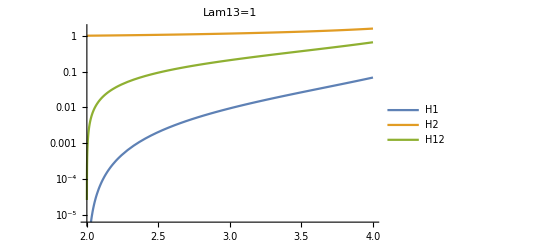

```mathematica
LogPlot[{LamH1[x]/.solA[[1]],LamH2[x]/.solA[[1]],LamH12[x]/.solA[[1]]},{x,2,4.0},PlotLegends->{"H1","H2","H12"},PlotLabel->"Lam13=1"]
```

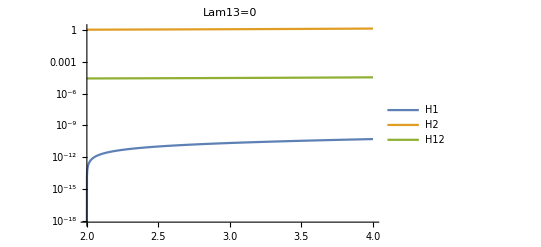

```mathematica
LogPlot[{LamH1[x]/.solB[[1]],LamH2[x]/.solB[[1]],LamH12[x]/.solB[[1]]},{x,2,4.0},PlotLegends->{"H1","H2","H12"},PlotLabel->"Lam13=0"]
```